## Referências

[1] artigo BP: Liberti,L., Lavor,C., Maculan,N., A branch-and-prune algorithm for the molecular distance geometry problem,Int.Trans.Oper.Res. 15 (2008),no.1,1–17(https://onlinelibrary.wiley.com/doi/full/10.1111/j.1475-3995.2007.00622.x)
 
[2]  pacote mdgp.nb:  https://github.com/michaelsouza/bioinfo/blob/master/codes/IMPA2017/mdgp.nb

## Instance Creation and Plot Routines

Instance Creation: DG
DGAllEdges, DGEdgeWeight, DGEdgeDistanceBounds, DGProblem, DGSaveProblem, DGGraphGetIJD

## Source Code

```mathematica
ClearAll[
DGAllEdges,
DGEdgeWeight,
DGEdgeDistanceBounds,
DGProblem,
DGPrintGraph,
DGPrintX,
DGSaveProblem,
DGGraphGetIJD
  ];

DGAllEdges[n_] := Module[{i, j, k = 0, pij},
   pij = Table[0, {i, (n (n - 1))/2}];
   For[i = 1, i <= n, i++,
    For[j = (i + 1), j <= n, j++,
      k++;
      pij[[k]] = i <-> j;
      ];
    ];
   Return[pij]
   ];

DGEdgeWeight[G_, E_] :=
  (* Gets edge weight. 'E' can be a single edge or a list of edges; *)
  Module[
{i, eij,wij, D = {}},
If[Not[FailureQ[PropertyValue[{G, E[[1]]}, EdgeWeight]]],
(* E is a list of edges *)
For[i = 1, i <= Length[E], i++,
eij = E[[i]];
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[wij=PropertyValue[{G, eij}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]];
AppendTo[D, wij]],
(* E is a single edge *)
eij = E;
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[D = PropertyValue[{G, E}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]]
];
Return[D]
];

DGEdgeDistanceBounds[G_, E_] := Module[
   {eij = E, Lij, Uij, Vij},
   If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
   Vij = PropertyValue[{G, eij}, "DistanceBounds"];
   Return[Vij]
   ];

DGProblem[x_,eij_: {},dijEps_: {}] :=
  (* Creates a problem P such that P["G"] is the problem graph and P["X"] is a problem solution; *)
  Module[{i,j,d,dij,k,numberOfAtoms,G,E,DijEps},
   (* set default values *)
   If[Length[eij]>0,E=eij,E=DGAllEdges[Length[x]]];
   If[Length[dijEps]>0,DijEps=dijEps,DijEps=Table[0,{i,Length[E]}]];
   (* unpacks the edges and calculate distances *)
   i=Table[E[[k]][[1]],{k,Length[E]}];
   j=Table[E[[k]][[2]],{k,Length[E]}];
   d=Table[N[Norm[x[[i[[k]]]] - x[[j[[k]]]]]], {k, Length[E]}];
   numberOfAtoms = Max[i, j];
   (* creates distance matrix *)
   G=Table[Infinity, {i, 1, numberOfAtoms}, {j, 1, numberOfAtoms}];
   For[k=1,k≤Length[i],k++,
      G[[i[[k]]]][[j[[k]]]]=d[[k]];
      G[[j[[k]]]][[i[[k]]]]=d[[k]]
    ];
   (* creates the graph *)
   G = WeightedAdjacencyGraph[G];
   (* adds distance bounds *)
   If[Length[DijEps]!=Length[i],Throw["InvalidInput: eij and dijEps must have the same size"]]; 
   For[k=1,k≤Length[i],k++,
    dij=DGEdgeWeight[G,i[[k]]<->j[[k]]];
    PropertyValue[{G,i[[k]]<->j[[k]]},"DistanceBounds"]={(1-DijEps[[k]]),(1+DijEps[[k]])}*dij
    ];
   Return[<|"X"->x,"G"->G|>];
   ];

DGPrintGraph[G_]:=Module[{edges,table,eij,i,j,k,Lij,Uij,Dij},
edges=EdgeList[G];
table=Table[0,{i,Length[edges]},{j,5}];
For[k=1,k≤Length[edges],k++,
eij=edges[[k]];
{i,j}={eij[[1]],eij[[2]]};
{Lij,Uij}=DGEdgeDistanceBounds[G,eij];
Dij=DGEdgeWeight[G,eij];
table[[k]]={i,j,Dij,Lij,Uij}
];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[edges]}],{"i","j","dij","lij","uij"}}]];
Return[TableForm[table,TableHeadings->{Table[i,{i,Length[edges]}],{"i","j","dij","lij","uij"}}]]
];

DGPrintX[X_]:=Print[TableForm[X, TableHeadings -> {Table[i, {i, Length[X]}], {"x", "y", "z"}}]]; 

DGPrintDistanceMatrix[X_,edges_]:=Module[{E=edges,table,i,j,k},
table=Table[{i=E[[k]][[1]],j=E[[k]][[2]],N[Norm[X[[i]]-X[[j]]]]},{k,Length[E]}];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[E]}], {"i","j","dij"}}]]
];
DGPrintDistanceMatrix[X_]:=Module[{edges},
edges=DGAllEdges[Length[X]];
DGPrintDistanceMatrix[X,edges]
];

DGSaveProblem[P_, fname_] :=
  (* Create the files fname.csv and fname_xsol.csv with, respectively, the DG constraints given by P["G"] and one associated solution P["X"] *)
  Module[{edges, fid, table, eij, i, j, k, X, G, Dij, Lij, Uij},
   (* creates and saves solution table *)
   table = Table[P["X"][[i]][[j]], {i, Length[P["X"]]}, {j, 3}];
   fid = StringJoin[fname, "_xsol.csv"];
   Print["Saving solution file ", fid];
   Export[fid, table, TableHeadings -> {"x", "y", "z"}];
   (* creates and saves constraints table *)
   G = P["G"];
   edges = EdgeList[G];
   table = Table[0, {i, Length[edges]}, {j, 5}];
   For[k = 1, k <= Length[edges], k++,
    eij = edges[[k]];
    {i, j} = {eij[[1]], eij[[2]]};
    {Lij, Uij} = DGEdgeDistanceBounds[G, eij];
    Dij = DGEdgeWeight[G, eij];
    table[[k]] = {i, j, N[Dij], N[Lij], N[Uij]}
    ];
   fid = StringJoin[fname, ".csv"];
   Print["Saving constraints file ", fid];
   Export[fid, table, TableHeadings -> {"I", "J", "D", "L", "U"}];
   ];

DGGraphGetIJD[G_]:=Module[{i,j,k,d,E},
E=EdgeList[G];
i=Table[E[[k]][[1]],{k,Length[E]}];
j=Table[E[[k]][[2]],{k,Length[E]}];
d=Table[DGEdgeWeight[G,E[[k]]],{k,Length[E]}];
Return[{i,j,d}];
]
```

Instance Creation: MDGP
DGSetXByCartesianSystem, DGSetXByHomogeneousCoords, DGRandom3DBackbone, DGRandomMDGP, DGCalculateProteinAngles, DGCalculateProteinAnglesForAtomAtPosition, DGCalculateTorsionAngles

## Source Code

```mathematica
ClearAll[
DGSetXByCartesianSystem,
DGSetXByHomogeneousCoords,
DGRandom3DBackbone,
DGRandomMDGP,
DGPlaneAndTorsionAngles
];
DGSetXByCartesianSystem[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using rotations and translations explicitly;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]) 
*)
Module[
(* declare local variables *)
{a,b,c,i,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[θ[[3]]],d[[3]]Sin[θ[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[θ[[i]],n]; (* rotation creation *)
v=R[v]; (* rotation apply *)
(* apply torsion rotation and translation *)
R=RotationTransform[ω[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
Return[X];
];

DGSetXByHomogeneousCoords[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using transformation matrices;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]); 
*)
Module[
{B,B1,B2,B3,X,i,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
{ct,st}={Cos[θ[[3]]],Sin[θ[[3]]]};
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]ct,d[[3]]st ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[θ[[i]]],Sin[θ[[i]]]};
{cw,sw}={Cos[ω[[i]]],Sin[ω[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
Return[X];
];

DGRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0]:=
(* Generates a random backbone in tridimensional Euclidean space;
   Input parameters;
   numberOfAtoms: number of 3D Euclidean points to be generated;
   algorithm: algorithm to be applied during coordinates calculation. The options 'are HomogeneousCoords' or 'CartesianSystem';
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on the current time is constructed;
 *)
Module[
(* declare the local variables *)
{d,θ,ω,X,output,ϵ=0.05},
(* set seed *)
If[seed>0,SeedRandom[seed]];
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{i,numberOfAtoms}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[RandomChoice[{60Degree,180Degree,300Degree}]*(1+RandomReal[{-ϵ,ϵ}]),{i,numberOfAtoms}];
ω[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=DGSetXByHomogeneousCoords[d,θ,ω],
"CartesianSystem",X=DGSetXByCartesianSystem[d,θ,ω],
_,Throw["InvalidAlgorithm:",OptionValue[algorithm]]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->ω,"CovalentBondLengths"->d,"PlaneRotationAngles"->θ|>
];

DGEdgesMDGP[numberOfAtoms_]:=Module[{i,j,edges={}},
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤Min[i+3,numberOfAtoms],j++,
AppendTo[edges,i<->j];
];
];
Return[edges];
];

DGRandomMDGP[numberOfAtoms_,dijEps_:0.0,dijMax_:Infinity,seed_:0]:=
(* Generates a random MDGP instance.; 
   numberOfAtoms: number of 3D Euclidean points to be generated;
   dijEps: the upper (uij) and lower (lij) constraints boundaries are generated using the formulae lij = (1-dijEps) and uij = (1+dijEps); 
   dijMax: all distances greater than dijMax are dropped;
   algorithm: defines the method (algorithm) used to calculate the pairwise distances. The options are "DistanceMatrix" and "Nearest";
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on current is constructed;
*)
Module[
(* declare local variables *)
{i,j,X,D,E,dij,DijEps},
X=DGRandom3DBackbone[numberOfAtoms,"HomogeneousCoords",seed]["Points"];
E={};
DijEps={};
(* set distance bounds *)
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤numberOfAtoms,j++,
(* exact distances *)
If[Abs[i-j]≤2,
AppendTo[E,{i,j}];
AppendTo[DijEps,0];
Continue[];
];
(* intervalar distances *)
If[Abs[i-j]==3||N[Norm[X[[i]]-X[[j]]]]<dijMax,
AppendTo[E,{i,j}];
AppendTo[DijEps,dijEps]
];
];
];
Return[DGProblem[X,E,DijEps]];
];

DGPlaneAndTorsionAngles[A_,B_,C_,D_,verbose_:False]:=
(* Calculates the plane and torsion for 3D points A, B, C and D in that order. *)
Module[
{nabc, nbcd,θ,ω},
(* centered at C *)
θ=VectorAngle[B-C,D-C];
If[verbose,Print["(θ):Angle[BCD]  =",θ]];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
ω=VectorAngle[nabc,nbcd];
If[verbose,Print["(ω):Angle[ABCD] =",ω]];
Return[{θ,ω}];
];

DGPlaneAndTorsionAngles[X_,i_]:=
(* Calculates plane and torsion angles of i-th atom. *)
DGPlaneAndTorsionAngles[X[[i-3]],X[[i-2]],X[[i-1]],X[[i]]];

DGPlaneAndTorsionAngles[X_]:=Module[
{θ,ω,i},
ω=Table[0,{i,Length[X]}];
θ=Table[0,{i,Length[X]}];
For[i=4,i≤Length[X],i++,
{θ[[i]],ω[[i]]}=DGPlaneAndTorsionAngles[X,i]
];
Return[{θ,ω}];
];
```

Plot Routines
DGPlot3DBackbone, DGPlotAdjacencyMatrix, DGByHandTreeFromBranches

## Source Code

```mathematica
ClearAll[
DGPlot3DBackbone,
DGPlotAdjacencyMatrix,
DGByHandTreeFromBranches
]

DGPlot3DBackbone[X_,r_,d_]:=Module[{objs={},single,k,Y},
(* Plots the points using the coordinates of X["Points"] property *)
single=Length[X[[1]][[1]]]==0;
If[single,Y={X},Y=X];
For[k=1,k≤Length[Y],k++,
objs=Union[objs,Table[{Red,Sphere[Y[[k]][[i]],r]},{i,3}]];
objs=Union[objs,Table[{Blue,Sphere[Y[[k]][[i]],r]},{i,3,Length[Y[[k]]]}]];
AppendTo[objs,{LightGray,Tube[Y[[k]],d]}];
];
Graphics3D[
objs,
 Axes->False,
Boxed->False, ViewPoint->Top]
]

DGPlotAdjacencyMatrix[G_,DiagonalCovering_:False]:=Module[
{i,j,n,ei,ej,edges,primitives,add},
n=Max[VertexList[G]];
edges=EdgeList[G];
(* inverting edges position *)
edges=Table[{edges[[i]][[2]],n-edges[[i]][[1]]+1},{i,Length[edges]}];
primitives={
{PointSize[Medium],Point[edges]},
{Red,Dashed,Line[{{1,n},{n,1}}]}
};
(* Plot diagonal covering *)
If[DiagonalCovering,
For[i=1,i≤Length[edges],i++,
add=True;
ei=edges[[i]];
For[j=1,j≤Length[edges],j++,
ej=edges[[j]];
If[(ej[[1]]==ei[[1]]&&ej[[2]]>ei[[2]]),add=False];
If[(ej[[2]]==ei[[2]]&&ej[[1]]>ei[[1]]),add=False];
];
If[add,
PrependTo[primitives,
{Opacity[0.2],Red,Triangle[{{ei[[1]],n+1-ei[[1]]},ei,{n+1-ei[[2]],ei[[2]]}}]}]
];
];
];

Graphics[primitives,
Axes->True,
GridLines->Automatic,
Ticks->{Automatic,Table[{i,n+1-i},{i,n}]},
AxesOrigin->{1,1}
]
Return[primitives];
];

(* exibe solução do BP em uma árvore binária *)
DGByHandTreeFromBranches[G_,branch_,branches_,check_]:=Module[
{T,X,k,i,n,b,x,y,z,dx,dy,dz,edges={},v={},styVertex,styEdges={},m,color,valid,nodes},
nodes=DGNaturalOrdering[G];
n=Length[VertexList[G]]-3;
(* creating edges *)
For[k=1,k≤2^n-1,k++,
AppendTo[edges,k<->2k];
AppendTo[edges,k<->2k+1];
];
(* highlighting current branch *)
For[k=0,k≤n,k++,
AppendTo[v,FromDigits[Join[{1},branch[[1;;k]]],2]];
If[k>0,
AppendTo[styEdges,v[[k]]<->v[[k+1]]->{Blue,Thickness[0.002]}]
];
];
(* coloring visited nodes (branches) *)
(*styVertex={LightGray};*)
styVertex={White};
If[Length[branches]>0,
For[k=1,k≤Length[branches],k++,
X=DGBPXinit[G,nodes[[1;;3]]];
b=branches[[k]];
If[check,
(* checking partial solutions *)
valid=True;
For[i=1,i≤n,i++,
X[[i+3]]=DGBPGetX[G,X,b[[i]],nodes,i+3];
If[valid&&DGRelativeResidue[G,X,nodes,i+3]<0.001,
color=Green,
valid =False;
(*color=Red;*)
color=Green;
];
v=FromDigits[Join[{1},b[[1;;i]]],2];
AppendTo[styVertex,v->color];
(*Print["[i] = ",i, ",  [k]= ",k,",  styVertex = ",styVertex];*)
],
(* checking only final solution *)
valid=True;
For[i=1,i≤n,i++,
X[[i+3]]=DGBPGetX[G,X,b[[i]],nodes,i+3];
If[DGRelativeResidue[G,X,nodes,i+3]>0.001,
valid=False
];
If[valid,color=Green,color=Red];
v=FromDigits[Join[{1},b],2];
AppendTo[styVertex,v->color]
],
];
];
];

T=TreeGraph[
edges,
VertexStyle->styVertex,
EdgeStyle->styEdges,
GraphLayout->{"LayeredEmbedding",LayerSizeFunction->(13&)},
VertexSize->1.1
];
Return[T];
];
```

## Check Solution and Standard Solvers

Solution Analysis 
DGRelativeResidue, DGLDME, DGRMSD

## Source Code

```mathematica
ClearAll[DGRelativeResidue,DGRMSD,DGLDME]
DGRelativeResidue[G_,X_,verbose_:False]:=Module[
{i,j,k,lij,uij, dij,numberOfEdges,E,error},
E=EdgeList[P["G"]];
numberOfEdges=Length[E];
error=Table[0,{i,numberOfEdges}];
For[k=1,k≤numberOfEdges,k++,
{i=E[[k]][[1]],j=E[[k]][[2]]};
{lij,uij}=DGEdgeDistanceBounds[G,i<->j];
dij=Norm[X[[i]]-X[[j]]];
error[[k]]=Max[Max[{0,lij-dij}]/lij,Max[{0,dij-uij}]/uij];
];
If[verbose,
Print["Solution Quality"];
Print["Number of nodes      : ",Length[X]];
Print["Number of edges      : ",Length[E]];
Print["Relative error bounds: ",{Min[error],Max[error]}];
Print["Mean relative error  : ",Mean[error]]];
Return[error]
];

DGRelativeResidue[G_,X_,nodes_,i_]:=
(* Calculates the relative residue of the nodes[[i]] considering only the nodes[[1;;i-1]] *)
Module[
(* local variables *)
{eij,j,k,V,Xi,Xj,Dij,Lij,Uij,errorDij,nid},
(* current position *)
Xi=X[[nodes[[i]]]];
(* indentifies which nodes has been already fixed *)
nid=Table[0,{k,i}];
For[k=1,k≤i,k++,
nid[[nodes[[k]]]]=k
];
(* considering only the precedent nodes *)
V= Select[AdjacencyList[G,nodes[[i]]],MemberQ[nid,#]&];
(*Print["V=",V];*)
errorDij=0.0;
For[k=1,k≤Length[V],k++,
(* neighbor index *)
j=V[[k]];
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
Dij=EuclideanDistance[Xi,Xj];
(* distance bounds *)
{Lij,Uij}=DGEdgeDistanceBounds[G,i<->j];
(* error Dij *)
eij=Max[(Lij-Dij)/Lij,(Dij-Uij)/Uij];
(* update error *)
If[eij>errorDij,errorDij=eij];
];
Return[errorDij]
];

DGLDME[G_,X_]:=Module[
{i,j,k,E,ldme=0,lij,uij,dij},
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
{lij,uij}=DGEdgeDistanceBounds[G,E[[k]]];
i=E[[k]][[1]];
j=E[[k]][[2]];
dij=Norm[X[[i]]-X[[j]],2];
ldme+=Max[lij-dij,dij-uij,0]^2
];
Return[Sqrt[ldme/Length[E]]]
];

DGRMSD[X_,Y_]:=Module[
{xc,yc,x,y,U,D,V,rmsd},
(* calculating centers *)
xc=Mean[X];
yc=Mean[Y];
(* translation *)
x=Table[X[[i]]-xc,{i,Length[X]}];
y=Table[Y[[i]]-yc,{i,Length[Y]}];
(* svd *)
V=Transpose[x].y;
{U,D,V}=SingularValueDecomposition[V];
V=U.Transpose[V];
x=x.V;
rmsd=Norm[x-y,"Frobenius"]/Sqrt[Length[x]];
Return[{rmsd,V,x,y}]
]
```

General Methods
DGNSolve, DGAllEdgesSolver, DGOptSolver

## DGNSolve - Nonlinear equations

### Source Code

```mathematica
ClearAll[DGNSolve]
DGNSolve[G_]:=Module[{k,i,j,d,d12,eqs,xi,xj,x,n},
{i,j,d}=DGGraphGetIJD[G];
eqs=Table[0,{k,Length[i]}];
n=Max[i,j];
x=Table[Symbol[StringJoin["x",ToString[xi],ToString[xj]]],{xi,n},{xj,3}];
For[k=1,k≤Length[i],k++,
xi=x[[i[[k]]]];
xj=x[[j[[k]]]];
eqs[[k]]=(xi[[1]]-xj[[1]])^2+(xi[[2]]-xj[[2]])^2+(xi[[3]]-xj[[3]])^2==d[[k]]^2
];
(* set some points *)
d12=DGEdgeWeight[G,1<->2];
eqs=Join[eqs,
{x[[1]][[1]]==0,x[[1]][[2]]==0,x[[1]][[3]]==0,
x[[2]][[1]]==d12,x[[2]][[2]]==0,x[[2]][[3]]==0}
];
Print["eqs=",TableForm[eqs]];
x=Flatten[x];
Quiet[x=NSolve[eqs,x,Reals]];
x=ArrayReshape[x,{n,3}];
Print["x=",TableForm[x]];
(* convert relations to scalar matrix *)
If[Length[x[[1]][[1]]]>1,x=Table[x[[i]][[j]][[2]],{i,n},{j,3}]];
Return[x]
];
```

## DGOptSolver - Optimization

### Source Code

```mathematica
ClearAll[DGOptSolverFobj,DGOptSolver]
```

```mathematica
DGOptSolverFobj[i_,j_,d_,x_]:=Module[{f=0,numberOfAtoms,ncols,nrows,k,y},
y=ArrayReshape[x,{Length[x]/3,3}];
For[k=1,k≤Length[d],k++,
f+=(d[[k]]^2-Norm[y[[i[[k]]]]-y[[j[[k]]]]]^2)^2
];
Return[f]
]
DGOptSolver[G_]:=Module[{numberOfAtoms,f,y,v,w,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
ClearAll[z];
y=Array[z,3*numberOfAtoms];
f:=DGOptSolverFobj[i,j,d,#]&;
{v,y}=NMinimize[f[y],y];
y=ArrayReshape[y,{Length[y]/3,3}];
y=Table[y[[iloc]][[jloc]][[2]],{iloc,Length[y]},{jloc,3}];
Return[y]
]
```

## DGAllEdgesSolver - Solver for complete distance matrices

### Source Code

```mathematica
ClearAll[DGAllEdgesSolver]
DGAllEdgesSolver[G_]:=Module[{numberOfAtoms,k,m,λ,v,x,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
(* creates distance matrix *)
m=Table[0,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
For[k=1,k≤Length[i],k++,
m[[i[[k]]]][[j[[k]]]]=d[[k]];
m[[j[[k]]]][[i[[k]]]]=d[[k]];
];
(* λ:eigenvalues and v:eigenvectors *)
m=Table[(m[[1]][[iloc]]^2+m[[1]][[jloc]]^2-m[[iloc]][[jloc]]^2)/2,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
{λ,v}=Eigensystem[m,3];
(* getting solution *)
x=Table[Sqrt[λ[[jloc]]]v[[jloc]][[iloc]],{iloc,numberOfAtoms},{jloc,3}];
Return[x]
]
```

## Ordering, BuildUP, BP

Ordering
DGOrdering, DGNaturalOrdering

## Source Code

```mathematica
ClearAll[DGOrdering,DGNaturalOrdering]
DGOrdering[G_,C_,verbose_:False]:=
(* Finds an order such that all atoms could be determined by following it; 
   C: Initial clique used to start the ordering;
   G: Instance graph;
*)
Module[{i,j,k,neighs,nAtoms,nFixedAtoms,nFixedNeighs,atomsToBeFixed,atomOrder, order,minNeighsToBeFixed},
(* initial values *)
minNeighsToBeFixed=Length[C];
nAtoms=Length[VertexList[G]];
nFixedNeighs=Table[0,{i,nAtoms}];
atomOrder=Table[0,{i,nAtoms}];
atomsToBeFixed=C;
nFixedNeighs[[C]]=Infinity;
nFixedAtoms=0;
While[Length[atomsToBeFixed]>0,
If[verbose,
Print["nFixedNeighs=",nFixedNeighs];
Print["atomsToBeFixed=",atomsToBeFixed];
];
i=First[atomsToBeFixed];
(* remove the first element *)
atomsToBeFixed=Rest[atomsToBeFixed];
(* skipped: already fixed *)
If[atomOrder[[i]]>0,Continue[]];
If[verbose,Print["Fixing: ",i]];
atomOrder[[i]]=++nFixedAtoms;
If[verbose,Print["atomOrder=",atomOrder]];
(* update neighs score *)
neighs=AdjacencyList[G,i];
If[verbose,Print["neighs=",neighs]];
For[k=1,k≤Length[neighs],k++,
j=neighs[[k]];
nFixedNeighs[[j]]++;
If[atomOrder[[j]]==0&&nFixedNeighs[[j]]≥minNeighsToBeFixed &&Not[MemberQ[atomsToBeFixed,j]],
AppendTo[atomsToBeFixed,j];
];
]
];
If[nFixedAtoms≠nAtoms,Throw["InvalidOrdering: It has not been possible the set ordering."]];
order=Table[i,{i,nAtoms}];
order[[atomOrder]]=order;
Return[order];
]

DGNaturalOrdering[G_]:=Array[#&,Length[VertexList[G]]];
```

Intersection of spheres
DGIntersect3Spheres, DGIntersect4Spheres

```mathematica
ClearAll[DGIntersect3Spheres,DGIntersect4Spheres];
DGIntersect3Spheres[a_,ra_,b_,rb_,c_,rc_]:=
(* Gets the 2 solutions of {||x-a||=ra,||x-b||=rb,||x-c||=rc};
   Input;
   a,b,c: sphere centers;
   ra,rb,rc: respective sphere radius;
   Output;   
   x: the two intersections (x[[1]]: positive chirality and x[[2]]: negative chirality);
 *)
Module[{n,A,x,p,dp,u,v,w,du,dv,dw,dpu,AbsCos,error},
(* select the most perpendicular vertex angle (stability) *)
(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];*)
AbsCos[u_,v_]:=Dot[u,v]/(Norm[u]*Norm[v]);
{u,v,w,du,dv,dw}=MinimalBy[{
{AbsCos[b-a,c-a],{a,b,c,ra,rb,rc}},
{AbsCos[c-b,a-b],{b,c,a,rb,rc,ra}},
{AbsCos[a-c,b-c],{c,a,b,rc,ra,rb}}
},First][[1]][[2]];
(* normal to the plane (u,v,w) *)
n=Normalize[Cross[v-u,w-u]];
A={v-u,w-u,n};
x={(Dot[v,v]-Dot[u,u]-dv^2+du^2)/2,(Dot[w,w]-Dot[u,u]-dw^2+du^2)/2,Dot[n,u]};
p=LinearSolve[A,x];
(* select the factor with minimal canceling effect (stability) *)
{u,du}=MaximalBy[{
{Abs[(ra-Norm[p-a])/ra],{a,ra}},
{Abs[(rb-Norm[p-b])/rb],{b,rb}},
{Abs[(rc-Norm[p-c])/rc],{c,rc}}
},First][[1]][[2]];
dpu=Norm[p-u];
dp=N[Sqrt[(du+dpu)*(du-dpu)]];
(*dp=Re[dp];*)
x={p+dp*n,p-dp*n};
(*Print[">>> 3 esferas: ",Style[x,Red]];*)
(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];
Print["p=",p,"  dp=",dp,"  x=",x];*)
(* calculating max relative errors of each solution *)
error=Table[Max[Abs[{(Norm[a-x[[i]]]-ra)/ra,(Norm[b-x[[i]]]-rb)/rb,(Norm[c-x[[i]]]-rc)/rc}]],{i,2}];
Return[{x,error}];
];

DGIntersect4Spheres[a_,ra_,b_,rb_,c_,rc_,d_,rd_]:=
Module[{x,error,errd1,errd2},
{x,error}=DGIntersect3Spheres[a,ra,b,rb,c,rc];
errd1=Abs[N[Norm[x[[1]]-d]]-rd];
errd2=Abs[N[Norm[x[[2]]-d]]-rd];
If[errd1<errd2,
x=x[[1]];
error=Max[error[[1]],errd1],
x=x[[2]];
error=Max[error[[2]],errd2]
];
(*Print[">>> 4 esferas: ",Style[x,Red]];*)
Return[{x,error}]
];
```

DGBuildUpSolver
DGBuildUpInitX, DGBuildUpSetX, DGBuildUpSolver

### Source Code

```mathematica
ClearAll[
DGBuildUpInitX,
DGBuildUpSetX,
DGBuildUpSolver
]

DGBuildUpInitX[G_,basis_]:=Module[
{i1,i2,i3,i4,d12,d13,d14,d23,d24,d34,A,X,X21,X31,X32,X41,X42,error},
{i1,i2,i3,i4}=basis;
{d12,d13,d14,d23,d24,d34}=DGEdgeWeight[G,{i1<->i2,i1<->i3,i1<->i4,i2<->i3,i2<->i4,i3<->i4}];
(* set the position of the four atoms in the basis *)
X=Table[{0,0,0},{i,Length[VertexList[G]]}];
X[[i2]][[1]]=d12;
X21=X[[i2]][[1]];
X[[i3]][[1]]=(d13^2-d23^2+X21^2)/(2*X21);
X31=X[[i3]][[1]];
X[[i3]][[2]]=Sqrt[d13^2-X31^2];
(*Print[" - - "];
Print[" > > X[[i1]] = ",X[[i1]],", d14 = ",d14, ", X[[i2]] = ",X[[i2]],", d24 = ",d24, ", X[[i3]] = ",X[[i3]], "d34 = ",d34];
Print[" - - "];*)
{X[[i4]],error}=DGIntersect3Spheres[X[[i1]],d14,X[[i2]],d24,X[[i3]],d34][[1]];
Return[X];
];

DGBuildUpSetX[G_,X_,nodes_,i_]:=Module[
{j,k,neighs,basis,x,i1,i2,i3,i4,d1,d2,d3,d4,error},
k=nodes[[i]];
neighs=Intersection[AdjacencyList[G,k],nodes[[1;;(i-1)]]];
If[Length[neighs]<4,Throw["InvalidOrder: There is not enough neighs to set a basis"]];
basis=Subsets[neighs,{4}];
For[j=1,j≤Length[basis],j++,
{i1,i2,i3,i4}=basis[[j]];
{d1,d2,d3,d4}=DGEdgeWeight[G,{i1<->k,i2<->k,i3<->k,i4<->k}];
{x,error}=DGIntersect4Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3,X[[i4]],d4];
If[error<10^(-3),Break];
];
If[error>10^(-3),Throw["InvalidSolution: A precise solution could not be found."]];
Return[x]
];

DGBuildUpSolver[G_,nodes_]:=Module[
{i,X},
X=DGBuildUpInitX[G,nodes[[1;;4]]];
(* set remaining atoms *)
For[i=5,i≤Length[X],i++,
X[[nodes[[i]]]]=DGBuildUpSetX[G,X,nodes,i]
];
Return[X]
];
```

DGBPSolver
DGBPXinit, DGBPGetX, DGBPSolver

## Source Code

```mathematica
ClearAll[DGBPXinit,DGBPGetX,DGBPSolver]
DGBPXinit[G_,basis_]:=Module[{a,b,c,numberOfAtoms,dab,dac,dbc,θ,X},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
(* three first atoms *)
{a,b,c}=basis[[1;;3]];
{dab,dac,dbc}=DGEdgeWeight[G,{a<->b,a<->c,b<->c}];
(* planar rotation angle for third atom *)
θ=ArcCos[(dab^2+dbc^2-dac^2)/(2*dab*dbc)];
(* set the position of the three first points *)
X[[{a,b,c}]]={{0,0,0},{-dab,0,0},{-dab+dbc*Cos[θ],dbc*Sin[θ] ,0}};
Return[X];
]

DGBPGetX[G_,X_,branch_,nodes_,i_]:=Module[
{j,k,neighs,x,error,i1,i2,i3,d1,d2,d3},
k=nodes[[i]];
neighs=Intersection[AdjacencyList[G,k],nodes[[1;;(i-1)]]];
If[Length[neighs]<3,Throw["InvalidOrder: There is not enough neighs to set a basis"]];
(*Print["neighs=",neighs," k=",k];*)
{i1,i2,i3}=neighs[[1;;3]];
{d1,d2,d3}=DGEdgeWeight[G,{i1<->k,i2<->k,i3<->k}];
{x,error}=DGIntersect3Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3];
Return[x[[branch+1]]]
];

DGBPSolver[G_,nodes_,onesol_:False,verbose_:False, plotInfos_:False ]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G. *)
Module[
(* local variables *)
{i,k,numberOfAtoms,prune,branch,X,S,work,error,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
X=DGBPXinit[G,nodes[[1;;3]]];
(* init BPTree *)
branch=Table[0,{i,numberOfAtoms}];branch[[1;;3]]=0;(*branch[[1;;3]]=1;*)
work=Table[0,{i,numberOfAtoms}];work[[1;;3]]=1;
(* solutions and branches *)
S=<|"Points"->{},"Branches"->{}|>;
k=4;
While[k>3,
work[[k]]++;
X[[nodes[[k]]]]=DGBPGetX[G,X,branch[[k]],nodes,k];
error=DGRelativeResidue[G,X,nodes,k];
prune=error>tol;
If[plotInfos,
Print["[bp] k=",k,"  branch=",branch,"  error=",NumberForm[error,{3,2}],"  prune=",prune];
DGPrintX[X[[nodes[[1;;k]]]]];
];
(* solution found *)
If[Not[prune]&&k==numberOfAtoms ,
AppendTo[S["Points"],X];
AppendTo[S["Branches"],branch];
If[onesol,Return[{S,work}]];
];
(* update tree node *)
prune=prune||k==Length[branch];
If[prune&&branch[[k]]==1,
While[k>3&&branch[[k]]==1,k--];
];
If[prune&&branch[[k]]==0,
branch[[k]]=1;
For[i=k+1,i≤Length[branch],i++,branch[[i]]=0];
];
If[Not[prune],k++];
];
If[verbose,
Print["DGBPSolver"];
Print["Number of solutions: ",Length[S["Points"]]]
];
Return[{S,work}]
];
```

## Artigo BP

## §1, 2

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

### Exemplo 1:

-Graphics-

#### Exemplo 1 a) Coordenadas cartesianas via coordenadas homogêneas:

```mathematica
(* length of covalent bonds *)
d=Table[1.526,{i,6}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{i,6}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[0,{i,6}];
ω[[{4,5,6}]]={π/2,π/3,π/6};
(* set the remaining 3d positions *)
Xcoord1=DGSetXByHomogeneousCoords[d,θ,ω];
```

```mathematica
Print["UnderBar[Resultado das coordenadas cartesianas obtidas via coordenadas homogêneas]"];
Print[Style[TableForm[Transpose[Xcoord1],TableHeadings->{{"x","y","z"},{"x1   ","x2   ","x3   ","x4   ","x5   ", "x6   "}} ],Red]];
```

UnderBar[Resultado das coordenadas cartesianas obtidas via coordenadas homogêneas]

| x1    | x2    | x3    | x4    | x5    | x6   
x | 0 | -1.526 | -2.03376 | -2.2027 | -3.20839 | -4.22129
y | 0 | 0 | 1.43905 | 1.91787 | 1.02266 | 0.486582
z | 0 | 0 | 0 | -1.43905 | -2.15728 | -1.14964

```mathematica
(* UnderBar[obs:]
DGSetXByHomogeneousCoords[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using transformation matrices;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]); 
*)
Module[
{B,B1,B2,B3,X,i,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
{ct,st}={Cos[θ[[3]]],Sin[θ[[3]]]};
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]ct,d[[3]]st ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[θ[[i]]],Sin[θ[[i]]]};
{cw,sw}={Cos[ω[[i]]],Sin[ω[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
Return[X]
];
*)
```

#### Exemplo 1 b) Coordenadas cartesianas via coordenadas internas:

```mathematica
Xcoord2=DGSetXByCartesianSystem[d,θ,ω];
Print["UnderBar[Resultado das coordenadas cartesianas obtidas via coordenadas internas]"];
Print[Style[TableForm[Transpose[Xcoord2],TableHeadings->{{"x","y","z"},{"x1   ","x2   ","x3   ","x4   ","x5   ", "x6   "}} ],Red]];
```

UnderBar[Resultado das coordenadas cartesianas obtidas via coordenadas cartesianas]

| x1    | x2    | x3    | x4    | x5    | x6   
x | 0 | -1.526 | -2.03376 | -2.2027 | -3.20839 | -4.22129
y | 0 | 0 | 1.43905 | 1.91787 | 1.02266 | 0.486582
z | 0 | 0 | 0 | -1.43905 | -2.15728 | -1.14964

```mathematica
(* UnderBar[obs:]
DGSetXByCartesianSystem[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using rotations and translations explicitly;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]) 
*)
Module[
(* declare local variables *)
{a,b,c,i,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[θ[[3]]],d[[3]]Sin[θ[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[θ[[i]],n]; (* rotation creation *)
v=R[v]; (* rotation apply *)
(* apply torsion rotation and translation *)
R=RotationTransform[ω[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
Return[X]
];*)
```

#### Exemplo 1 c) : Coordenadas internas via coordenadas homogêneas ou cartesianas

```mathematica
Print["\nUnderBar[Valores esperados]"];
Print["θ = ", θ];
Print["ω = ",N[ ω]];
Print[];
```

UnderBar[Valores esperados]

θ = {0,0,1.91,1.91,1.91,1.91}

ω = {0.,0.,0.,1.5708,1.0472,0.523599}

```mathematica
Print[];
Print["UnderBar[Resultado correspondente às coordenadas homogêneas]"];
{theta1,omega1}=DGPlaneAndTorsionAngles[Xcoord1];
Print["θ = ",Style[theta1,Red]];
Print["ω = ",Style[omega1,Red]];
Print[];
```

UnderBar[Resultado correspondente às coordenadas homogêneas]

θ = {0,0,0,1.91,1.91,1.91}

ω = {0,0,0,1.5708,1.0472,0.523599}

```mathematica
Print[];
Print["UnderBar[Resultado correspondente às coordenadas cartesianas]"];
{theta2,omega2}=DGPlaneAndTorsionAngles[Xcoord2];
Print["θ = ",Style[theta2,Red]];
Print["ω = ",Style[omega2,Red]];
Print[];
```

UnderBar[Resultado correspondente às coordenadas cartesianas]

θ = {0,0,0,1.91,1.91,1.91}

ω = {0,0,0,1.5708,1.0472,0.523599}

```mathematica
(* UnderBar[obs:]
DGPlaneAndTorsionAngles[X_]:=Module[
{θ,ω,i},
ω=Table[0,{i,Length[X]}];
θ=Table[0,{i,Length[X]}];
For[i=4,i≤Length[X],i++,
{θ[[i]],ω[[i]]}=DGPlaneAndTorsionAngles[X,i]
];
Return[{θ,ω}];
];
*)
```

## § 3

-Graphics-

### Exemplo 2:

#### Exemplo 2a) Gerando instâncias aleatoriamente:

```mathematica
n=6;
(* gera um DMDGP com n átomos e distância de corte Subscript[r, c] = 0 *)
P=DGRandomMDGP[n,0.0,5];
(* extrai as informações a serem usadas na instância G = (V, E, d) *)
G=P["G"];
(* exibe o grafo associado a instância G = (V, E, d) em forma de tabela *)
Print["UnderBar[G  =  (V,  E,  d)]"];
plotGrafo1a = DGPrintGraph[G];
Print["\n"];
```

UnderBar[G  =  (V,  E,  d)]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.8371 | 3.8371 | 3.8371
4 | 1 | 5 | 4.98232 | 4.98232 | 4.98232
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 3.83414 | 3.83414 | 3.83414
8 | 2 | 6 | 4.34469 | 4.34469 | 4.34469
9 | 3 | 4 | 1.526 | 1.526 | 1.526
10 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
11 | 3 | 6 | 2.89128 | 2.89128 | 2.89128
12 | 4 | 5 | 1.526 | 1.526 | 1.526
13 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
14 | 5 | 6 | 1.526 | 1.526 | 1.526

```mathematica
n=6;
(* gera um DMDGP com n átomos e distância de corte Subscript[r, c] = 0 *)
P=DGRandomMDGP[n,0.0,5];
(* extrai as informações a serem usadas na instância G = (V, E, d) *)
G=P["G"];
(* exibe o grafo associado a instância G = (V, E, d) em forma de tabela *)
Print["UnderBar[G  =  (V,  E,  d)]"];
plotGrafo2a= DGPrintGraph[G];
Print["\n"];
```

UnderBar[G  =  (V,  E,  d)]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.83481 | 3.83481 | 3.83481
4 | 1 | 5 | 4.38174 | 4.38174 | 4.38174
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.9462 | 2.9462 | 2.9462
8 | 2 | 6 | 4.35484 | 4.35484 | 4.35484
9 | 3 | 4 | 1.526 | 1.526 | 1.526
10 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
11 | 3 | 6 | 3.83875 | 3.83875 | 3.83875
12 | 4 | 5 | 1.526 | 1.526 | 1.526
13 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
14 | 5 | 6 | 1.526 | 1.526 | 1.526

```mathematica
Print[Style["UnderBar[Instâncias MDGP gerados aleatóriamente para n = 6]",Red]];
Style[Grid[Table[{plotGrafo1a,plotGrafo2a},1]],Red]
```

UnderBar[Instâncias MDGP gerados aleatóriamente para n = 6]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.8371 | 3.8371 | 3.8371
4 | 1 | 5 | 4.98232 | 4.98232 | 4.98232
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 3.83414 | 3.83414 | 3.83414
8 | 2 | 6 | 4.34469 | 4.34469 | 4.34469
9 | 3 | 4 | 1.526 | 1.526 | 1.526
10 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
11 | 3 | 6 | 2.89128 | 2.89128 | 2.89128
12 | 4 | 5 | 1.526 | 1.526 | 1.526
13 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
14 | 5 | 6 | 1.526 | 1.526 | 1.526 |  | i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.91973 | 2.91973 | 2.91973
4 | 1 | 5 | 4.28012 | 4.28012 | 4.28012
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 3.83806 | 3.83806 | 3.83806
8 | 2 | 6 | 4.97706 | 4.97706 | 4.97706
9 | 3 | 4 | 1.526 | 1.526 | 1.526
10 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
11 | 3 | 6 | 3.83745 | 3.83745 | 3.83745
12 | 4 | 5 | 1.526 | 1.526 | 1.526
13 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
14 | 5 | 6 | 1.526 | 1.526 | 1.526

#### Exemplo 2b): Gerando instâncias usando SeedRandom[]:

```mathematica
n=6;
semente = 42;
(* gera um DMDGP com n átomos e distância de corte Subscript[r, c] = 0 *)
P=DGRandomMDGP[n,0.0,5,semente];
(* extrai as informações a serem usadas na instância G = (V, E, d) *)
G=P["G"];
(* exibe o grafo associado a instância G = (V, E, d) em forma de tabela *)
Print["UnderBar[G  =  (V,  E,  d)]"];
plotGrafo1b=DGPrintGraph[G];
Print["\n"];
```

UnderBar[G  =  (V,  E,  d)]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.89877 | 2.89877 | 2.89877
4 | 1 | 5 | 4.32319 | 4.32319 | 4.32319
5 | 1 | 6 | 4.64461 | 4.64461 | 4.64461
6 | 2 | 3 | 1.526 | 1.526 | 1.526
7 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
8 | 2 | 5 | 3.83863 | 3.83863 | 3.83863
9 | 2 | 6 | 4.33562 | 4.33562 | 4.33562
10 | 3 | 4 | 1.526 | 1.526 | 1.526
11 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
12 | 3 | 6 | 2.91661 | 2.91661 | 2.91661
13 | 4 | 5 | 1.526 | 1.526 | 1.526
14 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
15 | 5 | 6 | 1.526 | 1.526 | 1.526

```mathematica
n=6;
semente = 42;
(* gera um DMDGP com n átomos e distância de corte Subscript[r, c] = 0 *)
P=DGRandomMDGP[n,0.0,5,semente];
(* extrai as informações a serem usadas na instância G = (V, E, d) *)
G=P["G"];
(* exibe o grafo associado a instância G = (V, E, d) em forma de tabela *)
Print["UnderBar[G  =  (V,  E,  d)]"];
plotGrafo2b = DGPrintGraph[G];
Print["\n"];
```

UnderBar[G  =  (V,  E,  d)]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.89877 | 2.89877 | 2.89877
4 | 1 | 5 | 4.32319 | 4.32319 | 4.32319
5 | 1 | 6 | 4.64461 | 4.64461 | 4.64461
6 | 2 | 3 | 1.526 | 1.526 | 1.526
7 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
8 | 2 | 5 | 3.83863 | 3.83863 | 3.83863
9 | 2 | 6 | 4.33562 | 4.33562 | 4.33562
10 | 3 | 4 | 1.526 | 1.526 | 1.526
11 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
12 | 3 | 6 | 2.91661 | 2.91661 | 2.91661
13 | 4 | 5 | 1.526 | 1.526 | 1.526
14 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
15 | 5 | 6 | 1.526 | 1.526 | 1.526

```mathematica
Print[Style["UnderBar[Instâncias MDGP gerados fixando a semente para n = 6]",Red]];
Style[Grid[Table[{plotGrafo1b,plotGrafo2b},1]],Red]
```

UnderBar[Instâncias MDGP gerados fixando a semente para n = 6]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.89877 | 2.89877 | 2.89877
4 | 1 | 5 | 4.32319 | 4.32319 | 4.32319
5 | 1 | 6 | 4.64461 | 4.64461 | 4.64461
6 | 2 | 3 | 1.526 | 1.526 | 1.526
7 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
8 | 2 | 5 | 3.83863 | 3.83863 | 3.83863
9 | 2 | 6 | 4.33562 | 4.33562 | 4.33562
10 | 3 | 4 | 1.526 | 1.526 | 1.526
11 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
12 | 3 | 6 | 2.91661 | 2.91661 | 2.91661
13 | 4 | 5 | 1.526 | 1.526 | 1.526
14 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
15 | 5 | 6 | 1.526 | 1.526 | 1.526 |  | i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.89877 | 2.89877 | 2.89877
4 | 1 | 5 | 4.32319 | 4.32319 | 4.32319
5 | 1 | 6 | 4.64461 | 4.64461 | 4.64461
6 | 2 | 3 | 1.526 | 1.526 | 1.526
7 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
8 | 2 | 5 | 3.83863 | 3.83863 | 3.83863
9 | 2 | 6 | 4.33562 | 4.33562 | 4.33562
10 | 3 | 4 | 1.526 | 1.526 | 1.526
11 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
12 | 3 | 6 | 2.91661 | 2.91661 | 2.91661
13 | 4 | 5 | 1.526 | 1.526 | 1.526
14 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
15 | 5 | 6 | 1.526 | 1.526 | 1.526

```mathematica
(* UnderBar[obs:]
DGRandomMDGP[numberOfAtoms_,dijEps_:0.0,dijMax_:Infinity,seed_:0]:=
(* Generates a random MDGP instance.; 
   numberOfAtoms: number of 3D Euclidean points to be generated;
   dijEps: the upper (uij) and lower (lij) constraints boundaries are generated using the formulae lij = (1-dijEps) and uij = (1+dijEps); 
   dijMax: all distances greater than dijMax are dropped;
   algorithm: defines the method (algorithm) used to calculate the pairwise distances. The options are "DistanceMatrix" and "Nearest";
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on current is constructed;
*)
Module[
(* declare local variables *)
{i,j,X,D,E,dij,DijEps},
X=DGRandom3DBackbone[numberOfAtoms,"HomogeneousCoords",seed]["Points"];
E={};
DijEps={};
(* set distance bounds *)
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤numberOfAtoms,j++,
(* exact distances *)
If[Abs[i-j]≤2,
AppendTo[E,{i,j}];
AppendTo[DijEps,0];
Continue[];
];
(* intervalar distances *)
If[Abs[i-j]==3||N[Norm[X[[i]]-X[[j]]]]<dijMax,
AppendTo[E,{i,j}];
AppendTo[DijEps,dijEps]
];
];
];
Return[DGProblem[X,E,DijEps]]
];*)
```

### Exemplo 3:

```mathematica
(* gera backbone com n átomos usando DGRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0] *)
n=6;
Xhomog=DGRandom3DBackbone[n];
(* exibe backbone gerado *)
Print[Style[Xhomog,Red]];
```

<|Points→{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.50034,2.16569,1.23131},{0.0244255,2.10459,1.23611},{0.561739,2.73129,-0.0473348}},TorsionAngles→{0,0,0,5.25639,0.999391,1.013},CovalentBondLengths→{0,1.526,1.526,1.526,1.526,1.526},PlaneRotationAngles→{0,0,1.91,1.91,1.91,1.91}|>

```mathematica
(* plota backbone gerado *)
graf = DGPlot3DBackbone[Xhomog["Points"],.2,.08]
```

-Graphics3D-

```mathematica
(*DGRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0]:=
(* Generates a random backbone in tridimensional Euclidean space;
   Input parameters;
   numberOfAtoms: number of 3D Euclidean points to be generated;
   algorithm: algorithm to be applied during coordinates calculation. The options 'are HomogeneousCoords' or 'CartesianSystem';
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on the current time is constructed;
 *)
Module[
(* declare the local variables *)
{d,θ,ω,X,output,ϵ=0.05},
(* set seed *)
If[seed>0,SeedRandom[seed]];
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{i,numberOfAtoms}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[RandomChoice[{60Degree,180Degree,300Degree}]*(1+RandomReal[{-ϵ,ϵ}]),{i,numberOfAtoms}];
ω[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=DGSetXByHomogeneousCoords[d,θ,ω],
"CartesianSystem",X=DGSetXByCartesianSystem[d,θ,ω],
_,Throw["InvalidAlgorithm:",OptionValue[algorithm]]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->ω,"CovalentBondLengths"->d,"PlaneRotationAngles"->θ|>
];*)
```

### Exercício 1:

Assim como no Exemplo 3, use o comando DGRandom3DBackbone[6] para gerar um backbone com n = 6 átomos. Verifique os argumentos na definição do módulo DGRandom3DBackbone[numberOfAtoms_, algorithm_: “HomogeneousCoords”, seed_: 0] e gere um backbone  com n = 6 átomos usando coordenadas cartesianas (“CartesianSystem”). Fixe a semente (seed), gere duas instâncias, uma usando coordenadas homogêneas e outra usando coordenadas cartesianas. Plote ambas soluções com DGPlot3DBackbone[ ]  e compare as soluções encontradas.

## § 3.1

-Graphics-

-Graphics-

-Graphics-

### Exemplo 4:

#### Exemplo 4 a) Testes com a instância lavor11_7 (gerando a instância e resolvendo com o BP):

```mathematica
(* define o conjunto das arestas E e F *)
Ed= {{1,2},{1,3},{1,4},
{2,3},{2,4},{2,5},
{3,4},{3,5},{3,6},
{4,5},{4,6},{4,7},
{5,6},{5,7},{5,8},
{6,7},{6,8},{6,9},
{7,8},{7,9},{7,10},
{8,9},{8,10},{8,11},
{9,10},{9,11},
{10,11}};
Ep= {{2,9},
{3,8},{3,9},{3,10},
{4,8},{4,9},{4,10},
{5,9},{5,10},
{6,10},
{7,11}
};
(* faz a união entre E e F *)
edges=Union[Ed,Ep];
(* gera de forma aleatória as posições da solução - usada para gerar a instância *)
X=DGRandom3DBackbone[11];
(* gera um MDGP com o DGProblem[] *)
P=DGProblem[X["Points"],edges];
(* extrai as informações a serem usadas na instância G = (V, E, d) *)
G=P["G"];
Print["UnderBar[G  =  (V,  E,  d)]"];
DGPrintGraph[G];
Print["\n"];
(* define uma ordem - a ordem natural *)
nodes=DGNaturalOrdering[G];
```

UnderBar[G  =  (V,  E,  d)]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.83481 | 3.83481 | 3.83481
4 | 2 | 3 | 1.526 | 1.526 | 1.526
5 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
6 | 2 | 5 | 2.9462 | 2.9462 | 2.9462
7 | 2 | 9 | 6.86691 | 6.86691 | 6.86691
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 3 | 6 | 3.83875 | 3.83875 | 3.83875
11 | 3 | 8 | 6.28917 | 6.28917 | 6.28917
12 | 3 | 9 | 6.62142 | 6.62142 | 6.62142
13 | 3 | 10 | 5.83524 | 5.83524 | 5.83524
14 | 4 | 5 | 1.526 | 1.526 | 1.526
15 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
16 | 4 | 7 | 3.83932 | 3.83932 | 3.83932
17 | 4 | 8 | 4.98278 | 4.98278 | 4.98278
18 | 4 | 9 | 5.21938 | 5.21938 | 5.21938
19 | 4 | 10 | 4.34847 | 4.34847 | 4.34847
20 | 5 | 6 | 1.526 | 1.526 | 1.526
21 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
22 | 5 | 8 | 3.83925 | 3.83925 | 3.83925
23 | 5 | 9 | 4.33422 | 4.33422 | 4.33422
24 | 5 | 10 | 3.88663 | 3.88663 | 3.88663
25 | 6 | 7 | 1.526 | 1.526 | 1.526
26 | 6 | 8 | 2.49139 | 2.49139 | 2.49139
27 | 6 | 9 | 2.92756 | 2.92756 | 2.92756
28 | 6 | 10 | 2.51838 | 2.51838 | 2.51838
29 | 7 | 8 | 1.526 | 1.526 | 1.526
30 | 7 | 9 | 2.49139 | 2.49139 | 2.49139
31 | 7 | 10 | 2.93851 | 2.93851 | 2.93851
32 | 7 | 11 | 4.36341 | 4.36341 | 4.36341
33 | 8 | 9 | 1.526 | 1.526 | 1.526
34 | 8 | 10 | 2.49139 | 2.49139 | 2.49139
35 | 8 | 11 | 3.83717 | 3.83717 | 3.83717
36 | 9 | 10 | 1.526 | 1.526 | 1.526
37 | 9 | 11 | 2.49139 | 2.49139 | 2.49139
38 | 10 | 11 | 1.526 | 1.526 | 1.526

```mathematica
(* UnderBar[obs.]:
F = { Subscript[d, i,j] : j < i-3 }
   = { Subscript[d, 2]_(,{9}) = {3.387634917}, 
    Subscript[d, 3,{8,9,10}] = {3.96678038, 3.003368265, 3.796280236},
    Subscript[d, 4,{8,9,10}] = {2.60830758, 2.102385055, 3.159309539},
    Subscript[d, 5,{9,10}] = {2.689078459, 3.132251169},
    Subscript[d, 6,{10}] = {3.557526815},
    Subscript[d, 7,{11}] = {3.228657023}
  },

E = {Subscript[d, i,{i-1,i-2,i-3}]}
= { 1.526, 2.491389536, 3.83929637,
      1.526, 2.491389536, 3.831422399,
      1.526, 2.491389536, 3.835602674,
      1.526, 2.491389535, 3.030585263,
	  1.526, 2.491389534, 2.899348439,
	  1.526, 2.491389535, 3.086914764,
	  1.526, 2.491389536, 2.788611167,
	  1.526, 2.491389536, 2.888815709,
	  1.526, 2.491389537,
	  1.526
}
*)
```

```mathematica
(* altera pesos nas arestas Ed *)
PropertyValue[{G, 1<-> 4}, EdgeWeight]=3.83929637;
PropertyValue[{G, 1<-> 4},"DistanceBounds"]={3.83929637,3.83929637};
PropertyValue[{G, 1<-> 3}, EdgeWeight]=2.491389536;
PropertyValue[{G, 1<-> 3},"DistanceBounds"]={2.491389536,2.491389536};
PropertyValue[{G, 2<-> 5}, EdgeWeight]=3.831422399;
PropertyValue[{G, 2<-> 5},"DistanceBounds"]={3.831422399,3.831422399};
PropertyValue[{G, 2<-> 4}, EdgeWeight]=2.491389536;
PropertyValue[{G, 2<-> 4},"DistanceBounds"]={2.491389536,2.491389536};
PropertyValue[{G, 3<-> 6}, EdgeWeight]=3.835602674;
PropertyValue[{G, 3<-> 6},"DistanceBounds"]={3.835602674,3.835602674};
PropertyValue[{G, 3<-> 5}, EdgeWeight]=2.491389536;
PropertyValue[{G, 3<-> 5},"DistanceBounds"]={2.491389536,2.491389536};
PropertyValue[{G, 4<-> 7}, EdgeWeight]=3.030585263;
PropertyValue[{G, 4<-> 7},"DistanceBounds"]={3.030585263,3.030585263};
PropertyValue[{G, 4<-> 6}, EdgeWeight]=2.491389535;
PropertyValue[{G, 4<-> 6},"DistanceBounds"]={2.491389535,2.491389535};
PropertyValue[{G, 5<-> 8}, EdgeWeight]=2.899348439;
PropertyValue[{G, 5<-> 8},"DistanceBounds"]={2.899348439,2.899348439};
PropertyValue[{G, 5<-> 7}, EdgeWeight]=2.491389534;
PropertyValue[{G, 5<-> 7},"DistanceBounds"]={2.491389534,2.491389534};
PropertyValue[{G, 6<-> 9}, EdgeWeight]=3.086914764;
PropertyValue[{G, 6<-> 9},"DistanceBounds"]={3.086914764,3.086914764};
PropertyValue[{G, 6<-> 8}, EdgeWeight]=2.491389535;
PropertyValue[{G, 6<-> 8},"DistanceBounds"]={2.491389535,2.491389535};
PropertyValue[{G, 7<-> 10}, EdgeWeight]=2.788611167;
PropertyValue[{G, 7<-> 10},"DistanceBounds"]={2.788611167,2.788611167};
PropertyValue[{G, 7<-> 9}, EdgeWeight]=2.491389536;
PropertyValue[{G, 7<-> 9},"DistanceBounds"]={2.491389536,2.491389536};
PropertyValue[{G, 8<-> 11}, EdgeWeight]=2.888815709;
PropertyValue[{G, 8<-> 11},"DistanceBounds"]={2.888815709,2.888815709};
PropertyValue[{G, 8<-> 10}, EdgeWeight]=2.491389536;
PropertyValue[{G, 8<-> 10},"DistanceBounds"]={2.491389536,2.491389536};
PropertyValue[{G, 9<-> 11}, EdgeWeight]=2.491389537;
PropertyValue[{G, 9<-> 11},"DistanceBounds"]={2.491389537,2.491389537};


(* altera pesos nas arestas Ep *)
PropertyValue[{G, 2<->9}, EdgeWeight]=3.387634917;
PropertyValue[{G, 2<-> 9},"DistanceBounds"]={3.387634917,3.387634917};
PropertyValue[{G, 3<->8}, EdgeWeight]=3.96678038;
PropertyValue[{G, 3<-> 8},"DistanceBounds"]={3.96678038,3.96678038};
PropertyValue[{G, 3<->9}, EdgeWeight]=3.003368265;
PropertyValue[{G, 3<-> 9},"DistanceBounds"]={3.003368265,3.003368265};
PropertyValue[{G, 3<->10}, EdgeWeight]=3.796280236;
PropertyValue[{G, 3<-> 10},"DistanceBounds"]={3.796280236,3.796280236};
PropertyValue[{G, 4<->8}, EdgeWeight]=2.60830758;
PropertyValue[{G, 4<-> 8},"DistanceBounds"]={2.60830758,2.60830758};
PropertyValue[{G, 4<->9}, EdgeWeight]=2.102385055;
PropertyValue[{G, 4<-> 9},"DistanceBounds"]={2.102385055,2.102385055};
PropertyValue[{G, 4<->10}, EdgeWeight]=3.159309539;
PropertyValue[{G, 4<-> 10},"DistanceBounds"]={3.159309539,3.159309539};
PropertyValue[{G, 5<->9}, EdgeWeight]=2.689078459;
PropertyValue[{G, 5<-> 9},"DistanceBounds"]={2.689078459,2.689078459};
PropertyValue[{G, 5<->10}, EdgeWeight]=3.132251169;
PropertyValue[{G, 5<-> 10},"DistanceBounds"]={3.132251169,3.132251169};
PropertyValue[{G, 6<->10}, EdgeWeight]=3.557526815;
PropertyValue[{G, 6<-> 10},"DistanceBounds"]={3.557526815,3.557526815};
PropertyValue[{G, 7<->11}, EdgeWeight]=3.228657023;
PropertyValue[{G, 7<-> 11},"DistanceBounds"]={3.228657023,3.228657023};
```

```mathematica
(* exibe o grafo associado a instância G = (V, E, d) em forma de tabela *)
Print["\n"];
Print["UnderBar[G  =  (V,  E,  d)]"];
plotGrafo = DGPrintGraph[G];
Print["\n"];
```

UnderBar[G  =  (V,  E,  d)]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.8393 | 3.8393 | 3.8393
4 | 2 | 3 | 1.526 | 1.526 | 1.526
5 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
6 | 2 | 5 | 3.83142 | 3.83142 | 3.83142
7 | 2 | 9 | 3.38763 | 3.38763 | 3.38763
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 3 | 6 | 3.8356 | 3.8356 | 3.8356
11 | 3 | 8 | 3.96678 | 3.96678 | 3.96678
12 | 3 | 9 | 3.00337 | 3.00337 | 3.00337
13 | 3 | 10 | 3.79628 | 3.79628 | 3.79628
14 | 4 | 5 | 1.526 | 1.526 | 1.526
15 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
16 | 4 | 7 | 3.03059 | 3.03059 | 3.03059
17 | 4 | 8 | 2.60831 | 2.60831 | 2.60831
18 | 4 | 9 | 2.10239 | 2.10239 | 2.10239
19 | 4 | 10 | 3.15931 | 3.15931 | 3.15931
20 | 5 | 6 | 1.526 | 1.526 | 1.526
21 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
22 | 5 | 8 | 2.89935 | 2.89935 | 2.89935
23 | 5 | 9 | 2.68908 | 2.68908 | 2.68908
24 | 5 | 10 | 3.13225 | 3.13225 | 3.13225
25 | 6 | 7 | 1.526 | 1.526 | 1.526
26 | 6 | 8 | 2.49139 | 2.49139 | 2.49139
27 | 6 | 9 | 3.08691 | 3.08691 | 3.08691
28 | 6 | 10 | 3.55753 | 3.55753 | 3.55753
29 | 7 | 8 | 1.526 | 1.526 | 1.526
30 | 7 | 9 | 2.49139 | 2.49139 | 2.49139
31 | 7 | 10 | 2.78861 | 2.78861 | 2.78861
32 | 7 | 11 | 3.22866 | 3.22866 | 3.22866
33 | 8 | 9 | 1.526 | 1.526 | 1.526
34 | 8 | 10 | 2.49139 | 2.49139 | 2.49139
35 | 8 | 11 | 2.88882 | 2.88882 | 2.88882
36 | 9 | 10 | 1.526 | 1.526 | 1.526
37 | 9 | 11 | 2.49139 | 2.49139 | 2.49139
38 | 10 | 11 | 1.526 | 1.526 | 1.526

```mathematica
(* resolve a instância com o algoritmo BP (DGBPSolver[]) e calcula o tempo (em [s]) usado nesta tarefa *)
timeElapsed=Timing[{S,work}=DGBPSolver[G,nodes,False,True]][[1]];
Print["UnderBar[Time elapsed] = ",Style[timeElapsed,Red]];
Print["\n"];
(* calcula o erro da primeira solução *)
DGRelativeResidue[G,S["Points"][[1]],True];
(* extrai de S a lista dos pontos X correspondentes a cada solução do problema *)
X=S["Points"];
(* extrai de S a lista dos caminhos B correspondentes a cada solução do problema *)
B=S["Branches"];
(* exibe soluções, caminhos que levaram as soluções e informações sobre a árvore do BP *)
Print["\n"];
Print["UnderBar[Soluções]"];
Print[Style[MatrixForm[X],Red]];
Print["\n"];
Print["UnderBar[Caminhos das soluções]"];
Print[Style[MatrixForm[B],Red]];
```

DGBPSolver

Number of solutions: 4

UnderBar[Time elapsed] = 0.109375

Solution Quality

Number of nodes      : 11

Number of edges      : 38

Relative error bounds: {0.,6.45041×10^-9}

Mean relative error  : 9.79518×10^-10

UnderBar[Soluções]

((0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55893
1.43934
-0.0502221) | (-4.0749
2.85363
0.19926) | (-5.58431
2.88988
-0.0222217) | (-6.2803
2.1201
1.09657) | (-5.76253
0.684877
1.12374) | (-4.36238
0.661601
1.73012) | (-4.34868
1.49515
3.00828) | (-5.39835
0.957243
3.97653)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55893
1.43934
-0.0502221) | (-4.05846
2.85943
-0.300212) | (-5.57919
2.89169
-0.17772) | (-6.19949
2.14861
-1.35744) | (-5.67996
0.714013
-1.38379) | (-4.24293
0.703747
-1.89713) | (-4.14582
1.56672
-3.15193) | (-5.12911
1.05224
-4.19936)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55893
1.43934
0.0502221) | (-4.05846
2.85943
0.300212) | (-5.57919
2.89169
0.17772) | (-6.19949
2.14861
1.35744) | (-5.67996
0.714013
1.38379) | (-4.24293
0.703747
1.89713) | (-4.14582
1.56672
3.15193) | (-5.12911
1.05224
4.19936)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55893
1.43934
0.0502221) | (-4.0749
2.85363
-0.19926) | (-5.58431
2.88988
0.0222217) | (-6.2803
2.1201
-1.09657) | (-5.76253
0.684877
-1.12374) | (-4.36238
0.661601
-1.73012) | (-4.34868
1.49515
-3.00828) | (-5.39835
0.957243
-3.97653))

UnderBar[Caminhos das soluções]

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1)

#### Exemplo 4 b): Testes com a instância lavor11_7 (comparando as soluções visualmente):

```mathematica
X=S["Points"];
graf = DGPlot3DBackbone[X,.2,.08];
graf1 = DGPlot3DBackbone[X[[1,;;]],.2,.08];
graf2 = DGPlot3DBackbone[X[[2,;;]],.2,.08];
graf3 = DGPlot3DBackbone[X[[3,;;]],.2,.08];
graf4 = DGPlot3DBackbone[X[[4,;;]],.2,.08];
Grid[Table[{graf1,graf2,graf3,graf4, graf},1]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

-Graphics-

#### Exemplo 4 c) Testes com a instância lavor11_7 (as soluções na árvore BP):

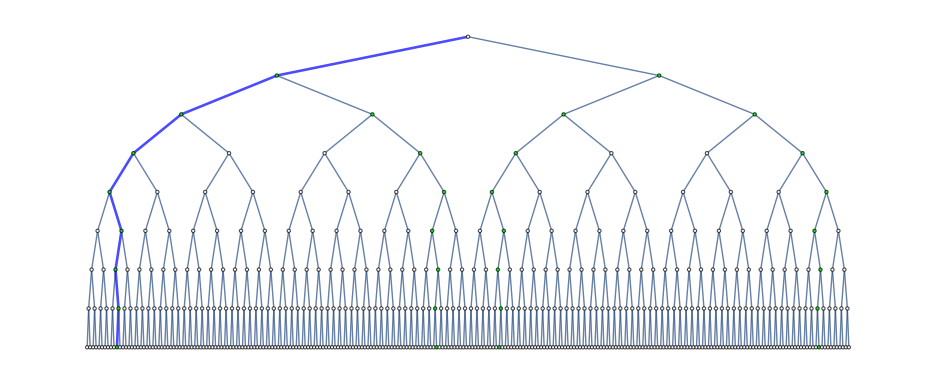

```mathematica
plot1 = DGByHandTreeFromBranches[P["G"],B[[1,4;;]],B[[;;,4;;]],True]
```

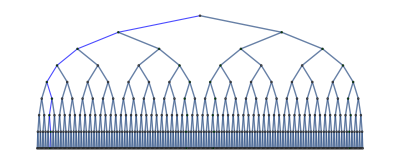
| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.8393 | 3.8393 | 3.8393
4 | 2 | 3 | 1.526 | 1.526 | 1.526
5 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
6 | 2 | 5 | 3.83142 | 3.83142 | 3.83142
7 | 2 | 9 | 3.38763 | 3.38763 | 3.38763
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 3 | 6 | 3.8356 | 3.8356 | 3.8356
11 | 3 | 8 | 3.96678 | 3.96678 | 3.96678
12 | 3 | 9 | 3.00337 | 3.00337 | 3.00337
13 | 3 | 10 | 3.79628 | 3.79628 | 3.79628
14 | 4 | 5 | 1.526 | 1.526 | 1.526
15 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
16 | 4 | 7 | 3.03059 | 3.03059 | 3.03059
17 | 4 | 8 | 2.60831 | 2.60831 | 2.60831
18 | 4 | 9 | 2.10239 | 2.10239 | 2.10239
19 | 4 | 10 | 3.15931 | 3.15931 | 3.15931
20 | 5 | 6 | 1.526 | 1.526 | 1.526
21 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
22 | 5 | 8 | 2.89935 | 2.89935 | 2.89935
23 | 5 | 9 | 2.68908 | 2.68908 | 2.68908
24 | 5 | 10 | 3.13225 | 3.13225 | 3.13225
25 | 6 | 7 | 1.526 | 1.526 | 1.526
26 | 6 | 8 | 2.49139 | 2.49139 | 2.49139
27 | 6 | 9 | 3.08691 | 3.08691 | 3.08691
28 | 6 | 10 | 3.55753 | 3.55753 | 3.55753
29 | 7 | 8 | 1.526 | 1.526 | 1.526
30 | 7 | 9 | 2.49139 | 2.49139 | 2.49139
31 | 7 | 10 | 2.78861 | 2.78861 | 2.78861
32 | 7 | 11 | 3.22866 | 3.22866 | 3.22866
33 | 8 | 9 | 1.526 | 1.526 | 1.526
34 | 8 | 10 | 2.49139 | 2.49139 | 2.49139
35 | 8 | 11 | 2.88882 | 2.88882 | 2.88882
36 | 9 | 10 | 1.526 | 1.526 | 1.526
37 | 9 | 11 | 2.49139 | 2.49139 | 2.49139
38 | 10 | 11 | 1.526 | 1.526 | 1.526 | -Graphics-

```mathematica
(* plota uma solução na árvore BP e os dados de entrada *)
Grid[Table[{plotGrafo,plot1},1]]
```

## § 4.1-4.3

-Graphics-

-Graphics-

- testbed: https : // en.wikipedia.org/wiki/Testbed

-Graphics-

-Graphics-

-Graphics-

-Graphics-

### Exemplo 5:

#### Exemplo 5 a) Gerando uma instância e resolvendo com o algoritmo BP e o BuildUp:

```mathematica
(* gera uma instância MDGP com n átomos *)
n=10;
P=DGRandomMDGP[n,0,5];
(*define uma ordem-a ordem natural*)
nodes=DGNaturalOrdering[P["G"]];
```

```mathematica
(* resolve a instância com o algoritmo BP (DGBPSolver[]) e calcula o tempo (em[s]) usado nesta tarefa
UnderBar[obs:] DGBPSolver[G_,nodes_,onesol_:False,verbose_:False, plotInfos_:False ]:=[...] *)
Print["UnderBar[Algoritmo BP]"]
timeElapsedBP=Timing[{S,work}=DGBPSolver[P["G"],nodes,True]][[1]];
Print["Time Elapsed BP = ",Style[timeElapsedBP,Red]];
(* calcula o erro da primeira solução *)
DGRelativeResidue[P["G"],S["Points"][[1]],True];
Print["\n"];
```

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.015625

Solution Quality

Number of nodes      : 10

Number of edges      : 32

Relative error bounds: {0.,2.0677×10^-14}

Mean relative error  : 1.75775×10^-15

```mathematica
(* resolver a instância com o algoritmo BP (DGBPSolver[]) e calcula o tempo (em[s]) usado nesta tarefa
UnderBar[obs:] DGBPSolver[G_,nodes_,onesol_:False,verbose_:False, plotInfos_:False ]:=[...] *)
Print["UnderBar[Algoritmo Build Up]"]
timeElapsedBU=Timing[Sb=DGBuildUpSolver[P["G"],nodes]][[1]];
Print["Time Elapsed Build Up = ",Style[timeElapsedBU,Red]];
(* calcula o erro da primeira solução *)
DGRelativeResidue[P["G"],Sb,True];
Print["\n"];
```

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.015625

Solution Quality

Number of nodes      : 10

Number of edges      : 32

Relative error bounds: {0.,4.74355×10^-14}

Mean relative error  : 2.54274×10^-15

#### Exemplo 5 b) Comparando as soluções obtidas visualmente:

```mathematica
(* exibe a quantidade de soluções *)
X=S["Points"];
(*Print["X = ",Style[X,Red]];*)
(*Print["X = ",Style[Sb,Red]];*)
Print["|X| = ", Style[Length[X],Red]];
```

|X| = 1

```mathematica
(* plota as soluções X *)
plotSolucaoBP = DGPlot3DBackbone[X[[1,;;]],.2,.08];
plotSolucaoBU = DGPlot3DBackbone[Sb,.2,.08];
Grid[Table[{plotSolucaoBP,plotSolucaoBU},1]]
```

-Graphics3D- | -Graphics3D-

```mathematica
Print[">> X_BP = ", Style[MatrixForm[Transpose[X[[1,;;]]]],Red], "\n>> X_BU = ", Style[MatrixForm[Transpose[Sb]],Red]];
```

>> X_BP = (0 | -1.526 | -2.03376 | -3.55919 | -4.06767 | -3.33504 | -3.30553 | -2.46385 | -0.99648 | -0.828194
0 | 0 | 1.43905 | 1.43925 | 2.8778 | 3.69493 | 2.91511 | 3.67305 | 3.62776 | 4.33067
0 | 0 | 0 | -0.0414366 | -0.0149084 | -1.0752 | -2.38657 | -3.40921 | -2.99274 | -1.64876)
>> X_BU = (0 | 1.526 | 2.03376 | 3.55919 | 4.06767 | 3.33504 | 3.30553 | 2.46385 | 0.99648 | 0.828194
0 | 0 | 1.43905 | 1.43925 | 2.8778 | 3.69493 | 2.91511 | 3.67305 | 3.62776 | 4.33067
0 | 0 | 0 | 0.0414366 | 0.0149084 | 1.0752 | 2.38657 | 3.40921 | 2.99274 | 1.64876)

#### Exemplo 5c) Analisando os erros das soluções:

```mathematica
Print["UnderBar[Algoritmo BP]"]
timeElapsedBP=Timing[{S,work}=DGBPSolver[P["G"],nodes,False]][[1]];
Print["Time Elapsed BP = ",Style[timeElapsedBP,Red]];
(* exibe a quantidade de soluções *)
X=S["Points"];
Print["|X| = ", Style[Length[X],Red]];
```

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.046875

|X| = 2

```mathematica
(* plota as soluções X *)
plotSolucao1BP = DGPlot3DBackbone[X[[1,;;]],.2,.08];
plotSolucao2BP = DGPlot3DBackbone[X[[2,;;]],.2,.08];
plotSolucaoBU = DGPlot3DBackbone[Sb,.2,.08];
Grid[Table[{plotSolucao1BP,plotSolucao2BP,plotSolucaoBU},1]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
(* calcula erro das soluções *)
Print["UnderBar[Algoritmo BP]"]
Print["UnderBar[solução 1:]"]
DGRelativeResidue[P["G"],X[[1,;;]],True];
Print["UnderBar[solução 2:]"]
DGRelativeResidue[P["G"],X[[2,;;]],True];
Print[];
Print["UnderBar[Algoritmo Build Up]"]
DGRelativeResidue[P["G"],Sb,True];
```

UnderBar[Algoritmo BP]

UnderBar[solução 1:]

Solution Quality

Number of nodes      : 10

Number of edges      : 32

Relative error bounds: {0.,2.0677×10^-14}

Mean relative error  : 1.75775×10^-15

UnderBar[solução 2:]

Solution Quality

Number of nodes      : 10

Number of edges      : 32

Relative error bounds: {0.,2.0677×10^-14}

Mean relative error  : 1.75775×10^-15

UnderBar[Algoritmo Build Up]

Solution Quality

Number of nodes      : 10

Number of edges      : 32

Relative error bounds: {0.,4.74355×10^-14}

Mean relative error  : 2.54274×10^-15

### Exemplo 6:

#### Exemplo 6 a) Comparando os algoritmos BP e BuildUp para n = 10, 11, 12, ..., 20:

10-11-12-13-14-15-16-17-18-19-20-

__ n = 10 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.015625

erro BP = 2.46622×10^-16

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.109375

erro BU = 1.10155×10^-15

..........

__ n = 11 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.015625

erro BP = 1.81498×10^-15

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.078125

erro BU = 2.11704×10^-15

..........

__ n = 12 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.015625

erro BP = 3.53839×10^-15

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.015625

erro BU = 9.88461×10^-15

..........

__ n = 13 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.015625

erro BP = 1.27359×10^-15

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.046875

erro BU = 2.52437×10^-15

..........

__ n = 14 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.015625

erro BP = 6.56662×10^-16

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.25

erro BU = 1.09504×10^-15

..........

__ n = 15 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.015625

erro BP = 1.44971×10^-13

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.109375

erro BU = 7.5463×10^-15

..........

__ n = 16 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.03125

erro BP = 8.59119×10^-14

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.5

erro BU = 4.10578×10^-14

..........

__ n = 17 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.03125

erro BP = 6.63908×10^-16

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.046875

erro BU = 1.0192×10^-14

..........

__ n = 18 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.03125

erro BP = 6.7854×10^-14

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 3.20313

erro BU = 6.95789×10^-13

..........

__ n = 19 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.03125

erro BP = 5.49899×10^-13

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.0625

erro BU = 1.19838×10^-14

..........

__ n = 20 __

UnderBar[Algoritmo BP]

Time Elapsed BP = 0.03125

erro BP = 5.71483×10^-16

UnderBar[Algoritmo Build Up]

Time Elapsed Build Up = 0.703125

erro BU = 7.45068×10^-15

..........

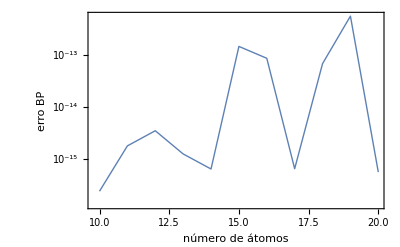

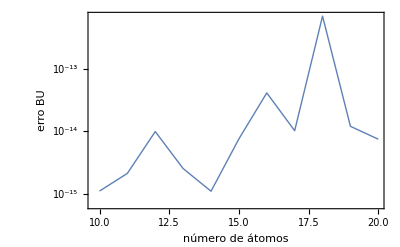

```mathematica
ListaErrosBP={};
ListaErrosBU={};
ListaTemposBP={};
ListaTemposBU={};
For[n=10,n≤20,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
TerrosBP={};TerrosBU={};
Print[];
Print["__ n = ",n," __"];
For[i=1,i≤1,i++, (* For[i=1,i≤5,i++, *)
(* gera uma instância MDGP com n átomos *)
P=DGRandomMDGP[n,0,5];
nodes=DGNaturalOrdering[P["G"]];
Print["UnderBar[Algoritmo BP]"];
timeElapsedBP=Timing[{S,work}=DGBPSolver[P["G"],nodes,True]][[1]];            Print["Time Elapsed BP = ",Style[timeElapsedBP,Red]];
(* calcula o erro da primeira solução *)
       erroBP = Mean[DGRelativeResidue[P["G"],S["Points"][[1]],False]];
TerrosBP=AppendTo[TerrosBP,erroBP];
Print["erro BP = ",Style[Mean[TerrosBP],Red]];
 Print["UnderBar[Algoritmo Build Up]"];
timeElapsedBU=Timing[Sb=DGBuildUpSolver[P["G"],nodes]][[1]];Print["Time Elapsed Build Up = ",Style[timeElapsedBU,Red]];
(* calcula o erro da primeira solução *)
 erroBU=Mean[DGRelativeResidue[P["G"],Sb,False]];
TerrosBU=AppendTo[TerrosBU,erroBU];
Print["erro BU = ",Style[Mean[TerrosBU],Red]];
];
   
Print[".........."];
ListaErrosBP=AppendTo[ListaErrosBP,{n,Mean[TerrosBP]}];
ListaErrosBU=AppendTo[ListaErrosBU,{n,Mean[TerrosBU]}];
];

(* plota gráficos de erros *)
ListLogPlot[ListaErrosBP,Joined->True,PlotStyle->Thick,Frame->True,FrameLabel->{"número de átomos","erro BP"},FrameStyle->Directive[Black,FontSize->13]]

ListLogPlot[ListaErrosBU,Joined->True,PlotStyle->Thick,Frame->True,FrameLabel->{"número de átomos","erro BU"},FrameStyle->Directive[Black,FontSize->13]]
```

#### Exemplo 6 b) Comparando os algoritmos BP e BuildUp para n = 5, 10, 15, ..., 60:

5-10-15-20-25-30-35-40-45-50-55-60-

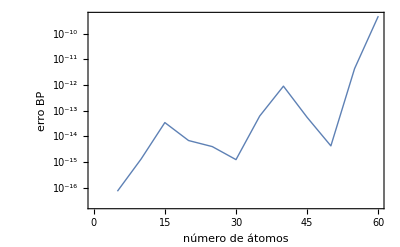

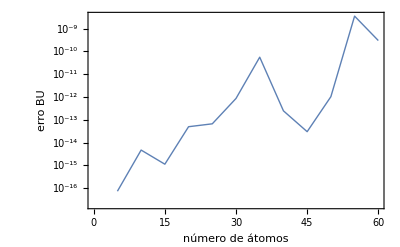

```mathematica
ListaErrosBP={};
ListaErrosBU={};
ListaTemposBP={};
ListaTemposBU={};
For[n=5,n≤60,n=n+5,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
TerrosBP={};TerrosBU={};
(*Print[];
Print["__ n = ",n," __"];*)
For[i=1,i≤1,i++, (* For[i=1,i≤5,i++, *)
(* gera uma instância MDGP com n átomos *)
P=DGRandomMDGP[n,0,5];
nodes=DGNaturalOrdering[P["G"]];
(*Print["UnderBar[Algoritmo BP]"];*)
timeElapsedBP=Timing[{S,work}=DGBPSolver[P["G"],nodes,True]][[1]];            (*Print["Time Elapsed BP = ",Style[timeElapsedBP,Red]];*)
(* calcula o erro da primeira solução *)
       erroBP = Mean[DGRelativeResidue[P["G"],S["Points"][[1]],False]];
TerrosBP=AppendTo[TerrosBP,erroBP];
(*Print["erro BP = ",Style[Mean[TerrosBP],Red]];
 Print["UnderBar[Algoritmo Build Up]"];*)
timeElapsedBU=Timing[Sb=DGBuildUpSolver[P["G"],nodes]][[1]];(*Print["Time Elapsed Build Up = ",Style[timeElapsedBU,Red]];*)
(* calcula o erro da primeira solução *)
 erroBU=Mean[DGRelativeResidue[P["G"],Sb,False]];
TerrosBU=AppendTo[TerrosBU,erroBU];
(*Print["erro BU = ",Style[Mean[TerrosBU],Red]];*)
];
   
(*Print[".........."];*)
ListaErrosBP=AppendTo[ListaErrosBP,{n,Mean[TerrosBP]}];
ListaErrosBU=AppendTo[ListaErrosBU,{n,Mean[TerrosBU]}];
];

(* plota gráficos de erros *)
ListLogPlot[ListaErrosBP,Joined->True,PlotStyle->Thick,Frame->True,FrameLabel->{"número de átomos","erro BP"},FrameStyle->Directive[Black,FontSize->13]]

ListLogPlot[ListaErrosBU,Joined->True,PlotStyle->Thick,Frame->True,FrameLabel->{"número de átomos","erro BU"},FrameStyle->Directive[Black,FontSize->13]]
```

### Exercício 2:

Altere os parâmetros do Exemplo 6 b) para testar resultados computacionais assim como foi feito na Tabela 1 (Table 1) do artigo sobre o BP. Teste os resultados para diferentes valores máximos de n (p. ex., n = 5, 10, 15, 20, 25, 30). Verifique se os resultados gerados estão de acordo, ou semelhantes, aos da Tabela 1 ou da Fig. 7.

### Exercício 3:

Implemente o módulo erro LDE, de acordo com o artigo sobre o BP.

### Exercício 4:

Repita o Exercício 2 considerando o erro LDE como medida de erro ao invés de Mean[DGRelativeResidue[...]]. Compare os novos resultados obtidos com os resultados do Exercício 2. O gráfico gerado está de acordo com a Fig. 7?

## § 4.4

-Graphics-

-Graphics-

-Graphics-

### Exercício 5:

Baseado no Exercício 2 e nas testes computacionais aqui vistos, busque testar as informações presentes nos dados exibidos na Tabela 2 (Table 2).

### Exercício 6:

Altere o código do Exemplo 6 b) para testar resultados computacionais com respeito ao tempo de processamento (CPU time). Plote gráficos dos tempos de processamente em função de cada n (p.ex., para variando em n = 5, 10, ... 30) , assim como foi feito quando se plotou os erros. Verifique se os resultados gerados estão de acordo, ou parecidos, com os da Tabela 1 e da Fig. 6.

### Exercício 7:

Utilizando os resultados já obtidos, tente testar computacionalmente com n = 10, 15, 20, ..., 70, 100, 200, 300, ..., 1000  as informações presentes na Tabela 1 e Fig. 6. Caso ao aumentar os valores de n surjam limitações computacionais, reduza o valor máximo de n de 1000 para um outro valor que seja menor e possibilite eliminar as limitações.

## § 5

### Exercício 8:

Repita o exercício 6 de forma a gerar os gráficos para a quantidade máxima de memória usada durante o processamento (MaxMemoryUsed[expr]) ao invés do erro.

(UnderBar[obs:] O comando MaxMemoryUsed[expr], fornece o número máximo de bytes usados durante o processamento do argumento expr.)